```mathematica
ClearAll["Global`*"];
```

```mathematica
f[t_,y_]:=t*(y^2)^(1/3);
```

```mathematica
(*Функция отклонения*)
```

```mathematica
calculateDifference[basicU_,concreteU_,m_]:=(
Res=Table[0,{m+1}];
Do[
Res[[i]]=Abs[concreteU[[i,2]]-basicU[[i,2]]],{i,1,m}
];
Print["Максимальное отклонение: ",Max[Res]];
Print["Точность: ",(Max[Res]/(2^4-1))];
MatrixForm[N[Res]]
);
```

```mathematica
(*Метод Рунге-Кутта явный*)
```

```mathematica
explicitRunge[t0_, tk_, y0_, m_]:=(
k1[h_, t_, y_]:=f[t,y];
k2[h_, t_, y_]:=f[t+0.5*h,y+0.5*h*k1[h,t,y]];
k3[h_, t_, y_]:=f[t+0.5*h,y+0.5*h*k2[h,t,y]];
k4[h_, t_, y_]:=f[t+h,y+h*k3[h,t,y]];
Print["Число шагов: ", m];
h=(tk-t0)/m;
Print["Шаг: ", h];
U=Table[0, {m+1},{2}];
U[[1,1]]=t0;
U[[1,2]]=y0;
t=t0;
y=y0;
Do[
dy=h*(k1[h,t,y]+2*k2[h,t,y]+2*k3[h,t,y]+k4[h,t,y])/6;
t=t+h;
y=y+dy;
U[[i,1]]=t;
U[[i,2]]=y,
{i,2,m+1}];
p=ListLinePlot[U];
Print[p];
U
);
```

Число шагов: 10

Шаг: 1/10

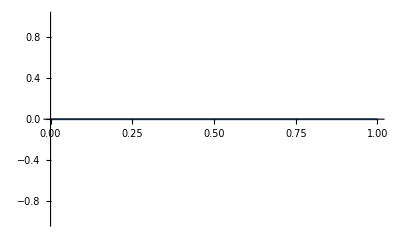

(0. | 0.
0.1 | 0.
0.2 | 0.
0.3 | 0.
0.4 | 0.
0.5 | 0.
0.6 | 0.
0.7 | 0.
0.8 | 0.
0.9 | 0.
1. | 0.)

```mathematica
basic=explicitRunge[0,1,0,10];
MatrixForm[N[basic]]
```

```mathematica
current=explicitRunge[0,1,0,15];
MatrixForm[N[current]]
```

Число шагов: 15

Шаг: 1/15

-Graphics-

(0. | 0.
0.0666667 | 0.
0.133333 | 0.
0.2 | 0.
0.266667 | 0.
0.333333 | 0.
0.4 | 0.
0.466667 | 0.
0.533333 | 0.
0.6 | 0.
0.666667 | 0.
0.733333 | 0.
0.8 | 0.
0.866667 | 0.
0.933333 | 0.
1. | 0.)

```mathematica
calculateDifference[basic,current,10]
```

Максимальное отклонение: 0.

Точность: 0.

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

```mathematica
(*Метод Рунге-Кутта неявный*)
```

```mathematica
implicitRunge[t0_,tk_, yk_, m_]:=(
k1[h_, t_, y_]:=f[t,y];
k2[h_, t_, y_]:=f[t-0.5*h,y-0.5*h*k1[h,t,y]];
k3[h_, t_, y_]:=f[t-0.5*h,y-0.5*h*k2[h,t,y]];
k4[h_, t_, y_]:=f[t-h,y-h*k3[h,t,y]];
Print["Число шагов: ", m];
h=(tk-t0)/m;
Print["Шаг: ", h];
U=Table[0, {m+1},{2}];
U[[1,1]]=tk;
U[[1,2]]=yk;
t=tk;
y=yk;
Do[
dy=h*(k1[h,t,y]+2*k2[h,t,y]+2*k3[h,t,y]+k4[h,t,y])/6;
t=t-h;
y=y-dy;
U[[i,1]]=t;
U[[i,2]]=y,
{i,2,m+1}];
p=ListLinePlot[U];
Print[p];
U
);
```

```mathematica
implicitRes=implicitRunge[0,1,0,15];
MatrixForm[N[implicitRes]]
```

Число шагов: 15

Шаг: 1/15

-Graphics-

(1. | 0.
0.933333 | 0.
0.866667 | 0.
0.8 | 0.
0.733333 | 0.
0.666667 | 0.
0.6 | 0.
0.533333 | 0.
0.466667 | 0.
0.4 | 0.
0.333333 | 0.
0.266667 | 0.
0.2 | 0.
0.133333 | 0.
0.0666667 | 0.
0. | 0.)

```mathematica
(* Метод Рунге-Кутта вложенный*)
```

```mathematica
nestedRunge[t0_,tk_, y0_, m_]:=(
k1[h_, t_, y_]:=f[t,y];
k2[h_, t_, y_]:=f[t+0.25*h,y+0.25*h*k1[h, t, y]];
k3[h_, t_, y_]:=f[t+(3/8)*h,y+(3/32)*h*k1[h, t, y]+(9/32)*h*k2[h, t, y]];
k4[h_, t_, y_]:=f[t+(12/13)*h,y+h*((1932/2197)*k1[h, t, y]-(7200/2197)*k2[h, t, y]+(7296/2197)*k3[h, t, y])];
k5[h_, t_, y_]:=f[t+h,y+h*((439/216)*k1[h, t, y]-8*k2[h, t, y]+(3680/513)*k3[h, t, y]-(845/4104)*k4[h, t, y])];
k6[h_, t_, y_]:=f[t+0.5*h,y-h*((8/27)*k1[h, t, y]+2*k2[h, t, y]-(3544/2565)*k3[h, t, y]+(1859/4104)*k4[h, t, y]-(11/40)*k5[h, t, y])];
Print["Число шагов: ",m];
h=(tk-t0)/m;
Print["Шаг: ",h];
t=t0;
y=y0;
U=Table[0,{m+1},{3}];
ForPlot=Table[0,{m+1},{2}];
U[[1,1]]=t0;
U[[1,2]]=y0;
U[[1,3]]=0;
ForPlot[[1,1]]=t0;
ForPlot[[1,2]]=y0;
Do[
dy=h*((25/216)*k1[h,t,y]*(1408/2565)*k3[h, t, y]+(2197/4104)*k4[h, t, y]-(1/5)*k5[h, t, y]);
t=t+h;
y=y+dy;
U[[i,1]]=t;
U[[i,2]]=y;
ForPlot[[i,1]]=t;
ForPlot[[i,2]]=y;
eps=h*(k1[h,t,y]/360-(128/4275)*k3[h,t,y]-(2197/75240)*k4[h,t,y]+k5[h,t,y]/50*(2/55)*k6[h,t,y]);
U[[i,3]]=eps,{i,2,m+1}];
p=ListLinePlot[ForPlot];
Print[p];
U
);
```

```mathematica
nestedRed=nestedRunge[0,1,0,15];
MatrixForm[N[nestedRed]]
```

Число шагов: 15

Шаг: 1/15

-Graphics-

(0. | 0. | 0.
0.0666667 | 0. | 0.
0.133333 | 0. | 0.
0.2 | 0. | 0.
0.266667 | 0. | 0.
0.333333 | 0. | 0.
0.4 | 0. | 0.
0.466667 | 0. | 0.
0.533333 | 0. | 0.
0.6 | 0. | 0.
0.666667 | 0. | 0.
0.733333 | 0. | 0.
0.8 | 0. | 0.
0.866667 | 0. | 0.
0.933333 | 0. | 0.
1. | 0. | 0.)

```mathematica
Clear[t,y];
```

```mathematica
(*Стандартный метод*)
```

```mathematica
explicitMathOp[t0_,tk_,y0_,m_]:=(
Y=NDSolve[{y'[t]==y[t]*(y[t]^2)^(1/3),y[t0]==0},y,{t,t0,tk},Method->"ExplicitRungeKutta"];
p=Plot[Evaluate[y[t]/.Y],{t,t0,tk}];
Print[p];
y[t_]=y[t]/.Y;
Print["Количество шагов: ",m];
h=(tk-t0)/m;
Print["Шаг: ",h];
t=t0;
U=Table[0,{m+1},{2}];
Do[
U[[i,1]]=t;
U[[i,2]]=y[t];
t+=h,
{i,1,m+1}
];
U
);
```

```mathematica
explicitMRes=explicitMathOp[0,1,0,15];
MatrixForm[explicitMRes]
```

-Graphics-

Количество шагов: 15

Шаг: 1/15

(0 | {0.}
1/15 | {0.}
2/15 | {0.}
1/5 | {0.}
4/15 | {0.}
1/3 | {0.}
2/5 | {0.}
7/15 | {0.}
8/15 | {0.}
3/5 | {0.}
2/3 | {0.}
11/15 | {0.}
4/5 | {0.}
13/15 | {0.}
14/15 | {0.}
1 | {0.})

```mathematica
calculateDifference[current,explicitMRes,15]
```

Максимальное отклонение: 0.

Точность: 0.

({0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
0.)

```mathematica
calculateDifference[Reverse[implicitRes],explicitMRes,15]
```

Максимальное отклонение: 0.

Точность: 0.

({0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
0.)

```mathematica
calculateDifference[nestedRed,explicitMRes,15]
```

Максимальное отклонение: 0.

Точность: 0.

({0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
0.)

```mathematica
Clear[t,y];
```

```mathematica
implicitMathOp[t0_,tk_,y0_,m_]:=(
Y=NDSolve[{y'[t]==y[t]*(y[t]^2)^(1/3),y[t0]==0},y,{t,t0,tk},Method->"ImplicitRungeKutta"];
p=Plot[Evaluate[y[t]/.Y],{t,t0,tk}];
Print[p];
y[t_]=y[t]/.Y;
Print["Количество шагов: ",m];
h=(tk-t0)/m;
Print["Шаг: ",h];
t=t0;
U=Table[0,{m+1},{2}];
Do[
U[[i,1]]=t;
U[[i,2]]=y[t];
t+=h,
{i,1,m+1}
];
U
);
```

```mathematica
implicitMRes=implicitMathOp[0,1,0,15];
MatrixForm[explicitMRes]
```

-Graphics-

Количество шагов: 15

Шаг: 1/15

(0 | {0.}
1/15 | {0.}
2/15 | {0.}
1/5 | {0.}
4/15 | {0.}
1/3 | {0.}
2/5 | {0.}
7/15 | {0.}
8/15 | {0.}
3/5 | {0.}
2/3 | {0.}
11/15 | {0.}
4/5 | {0.}
13/15 | {0.}
14/15 | {0.}
1 | {0.})

```mathematica
calculateDifference[current,implicitMRes,15]
```

Максимальное отклонение: 0.

Точность: 0.

({0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
0.)

```mathematica
calculateDifference[Reverse[implicitRes],implicitMRes,15]
```

Максимальное отклонение: 0.

Точность: 0.

({0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
0.)

```mathematica
calculateDifference[nestedRed,explicitMRes,15]
```

Максимальное отклонение: 0.

Точность: 0.

({0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
{0.}
0.)